## An introduction to the Wolfram Language for Minervans

Hello Minervans, 
Minerva just got a license for Mathematica/ the Wolfram Language/ WL (it’s the same thing) and this document and others that will follow are there to help you in making best use of the language for the Minerva curriculum.
You’ll quickly see that it can help you in many classes and has capabilities for many topics like Logic, Statistics, Calculus, Machine Learning, Graph Theory, Digital Humanities,...
I hope you’ll enjoy it and if you have any questions, feel free to email me at Katja.dellalibera@minerva.kgi.edu.

### The Basics: Syntax and running programs

To run anything in a Mathematica Notebook, just type your input and press [SHIFT]+[ENTER] to compute:

```mathematica
1412+851
```

2263

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

We have already come across some important syntax: Built-in functions in the Wolfram language start with a capital letter and are applied on some number of elements (in this case the integer 10) inside of square brackets [] resulting in an output (in this case a list from 1 to 10). Lists can be any number and combination of numbers, lists, strings, variables, etc and are marked by curly brackets {}

```mathematica
r=Range[10]; (*define r, but don't print it*)
```

If you don’t want your function to print immediately, simply put the “;” behind it. It will still evaluate and define the variable r. Comments look like this: (*comment*)

Display the variable r, you just defined

```mathematica
r
```

{1,2,3,4,5,6,7,8,9,10}

Use Length and % to get the length of the last output

```mathematica
Length[%]
```

10

To see r, simply type it in an input field and evaluate it. The symbol % will also return the last output, but generally it is better to define a variable. For those, the convention is using lowercase letters and words (Upper-case is reserved for built-in functions), and distinguishing multiple words using camel case (randomVariable, anotherRandomVariable,...)

### Getting Started

The notebooks are designed to help you enter Wolfram Language input:

If you start typing a function (or even just a word you think is related to what you are trying to do), it will automatically list functions starting with what you type. 
To learn more about any of them, simply click on the little i, next to them to open the documentation. It includes many useful examples, how to use them and related  functions, tutorials, or guides.
Strong Suggestion: DO NOT UNDERESTIMATE THE POWER OF THIS!!!
From my experience, 99% of the time, you can figure out how to do something just by typing a vaguely related word, and smartly clicking through the documentation. The Wolfram Language is a Knowledge Based Language. Over 5000 functions are built-in, so you don’t need to deal with importing libraries, each with their designs and conventions, etc.. Once you got the syntax down and can read the documentation, most of the pages will likely link you to what you need.

### Some more notes on Notebooks:

Mathematica notebooks are the original notebook environment. Jupyter notebooks were designed to be like Mathematica notebooks for Python, which also means you are going to find a lot of similarities. If you want to change the type of cell, open the drop-down menu [Format]→ [Style] to see all kinds of cells you can have and their shortcuts.

To the right, you can see layers of Square brackets, that you can double click on, to minimize a section, indicated by a section heading (a type of cell).
You don’t use laTex for formatting, although there are ways to translate from one to the other. If you want to write Math in Mathematica, they have their own system, which will be it’s own notebook. If you can’t wait to get started, check out the Fast Introduction for Math Students here.

If you mark a cell or group of cells and press [delete], they will be deleted, so be careful with that.

To open a new cell, simply press the down-arrow and start typing. The default will be a code cell.

### Why the Wolfram Language works especially well for Math

In Mathematics, we have a lot of terms we don’t know the values of. The Wolfram language can deal with symbolic input:

```mathematica
y+x+z
```

x+y+z

None of these variables are defined, but there won’t be an error, they are simply read as symbolic input. If I define one of them

```mathematica
y=2;
```

the function will now plug in the value of y defined.

```mathematica
y+x+z
```

2+x+z

Use ClearAll to Clear the variable y:

```mathematica
ClearAll[y]
```

It’s important to keep track of which variables you already defined and clear them if necessary, it can lead to weird bugs. Generally, if they turn black, they are already defined.
Another thing you can define are functions, with various in- and outputs.

Define f as a function that takes x as an input and outputs x^2+3.

```mathematica
f[x_]:= x^2 +3
```

So what can you do with your function?
Maybe you want to evaluate it at a certain point:

```mathematica
f[2]
```

7

Or you want to take the derivative?

```mathematica
f'[x]
```

2 x

You can also make a Table of the values f takes as x increases up to a value (10 in this case)

```mathematica
Table[f[x],{x,10}]
```

{4,7,12,19,28,39,52,67,84,103}

You might recognize the output of the function as a list, which is a data structure you will encounter rather frequently and is worth exploring a bit more.

### Lists:

Table is a frequently used function to generate lists or Lists of lists.

Use the function Table to generate a list of lists of x*y as x and y increase from 1 to 5:

```mathematica
Table[x*y,{x,5},{y,5}]
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20},{5,10,15,20,25}}

Ough, it is already quite hard to see what’s going on, since our array has 2 layers.
Lucky for us, an array with two layers like this can be displayed using Grid[]

```mathematica
Grid[Table[x*y,{x,5},{y,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

We are already using three functions stacked into each other and as you get more practice, you’ll see that a lot of Wolfram Language code will be functions wrapping one another.
If it gets really hard to see, you can put functions on new lines like this:

```mathematica
Grid[
Table[
x*y,
{x,5},{y,5}]
];
```

Let’s look at a few more things we can do with lists and learn a few functions in the process:

Use Table and RandomInteger to generate a list of random integers between 0 and 100.

```mathematica
randomList=Table[RandomInteger[100],10]
```

{74,53,82,6,35,80,80,98,72,79}

Access the 7th element of the list:

```mathematica
randomList[[7]] (*Two square brackets, not 1 like python*)
```

80

Sort the list:

```mathematica
Sort[randomList]
```

{6,35,53,72,74,79,80,80,82,98}

Plot the points from the list (the x-coordinate will default to the index) connected or not connected. :

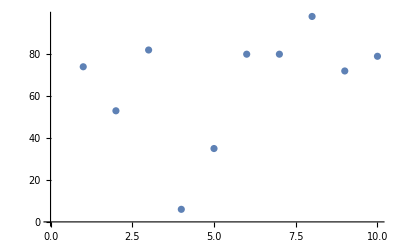
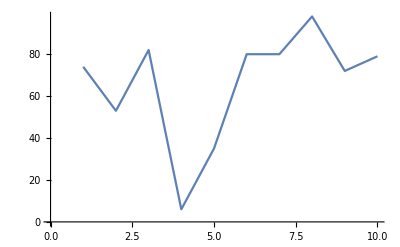

```mathematica
{ListPlot[randomList], ListLinePlot[randomList]}
```

You can see that even graphic elements such as plots can be elements in a lists.

### Visualizations

It is quite easy to plot all kinds of things in Mathematica. And if you take any kind of math or (social or natural) science class, it will come in quite handy.

#### Displaying Lists

You already saw how to display a list using ListPlot and ListLinePlot. 
Here are some other example charts:

A BarChart:

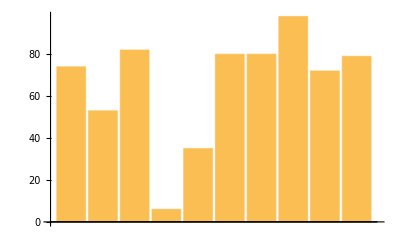

```mathematica
BarChart[randomList]
```

A PieChart:

```mathematica
PieChart[randomList]
```

-Graphics-

A NumberLinePlot:

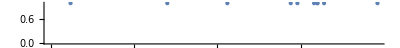

```mathematica
NumberLinePlot[randomList]
```

A Column (this is a bit like grid for one dimensional lists, Row will give you the same oriented horizontally):

```mathematica
Column[randomList]
```

74
53
82
6
35
80
80
98
72
79

Make a pie chart with 10 identical segments, each of size 1:

```mathematica
(*your code goes here*)
```

Make a bar chart of the sequence 1,2,3,...,9,10,9,8,7,...,1

```mathematica
(*your code goes here*)
```

#### Displaying functions:

You can plot not only lists, but functions.
Lets define a new function that takes two inputs, x and a. 
a_: 1 sets the default of a to 1

Define g[x,a]:

```mathematica
g[x_,a_:1]:= a*x^2 -1
```

Plot g[x] with a as the default 1.

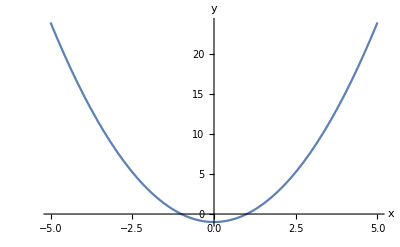

```mathematica
Plot[g[x],{x,-5,5},AxesLabel->{"x","y"}]
```

You may notice a third input in the function. Axislabel→ {“x”,”y”}  is an option for the Plot function that specifies the labels of the axes. There are a lot of options like setting a heading, colors, background, etc., but more on that later.

We can also change both x and a and create a 3D plot.

```mathematica
Plot3D[g[x,a],{x,-5,5},{a,-5,5},AxesLabel->{"x","a","g[x,a]"},PlotRange-> All]
```

-Graphics3D-

Can you tell what the PlotRange option does? Copy the code below and look at the function without it.

```mathematica
(*your code goes here*)
```

A 3D-plot is one way of showing how the factor a influences the graph of g[x], anther one is using an interactive feature of the Wolfram Language. This is especially true if you are dealing with more than 2 variables.

Instead of changing a in a Plot3D function, it is put inside of a Manipulate function.
Tip: If you want to see which brackets include what, simply click on a function multiple times. Everything inside of it will light up in blue.

```mathematica
Manipulate[Plot[g[x,a],{x,-5,5}],{a,-5,5,0.1},SaveDefinitions->True]
```

Play around with the slider in the graphic to watch it influence the graph. This can be really helpful observing how one or more variables change a function, especially if it is a complicated function with many factors. It also works in 3D.

#### Non-numeric Visualizations:

There are also ways to represent non-numeric data in the Wolfram Language. Word clouds for example. I’ve previously used them in assignments to represent qualitative answers to survey questions.

Import a text file of the Minerva’s website(just the front page) and create a WordCloud from it:

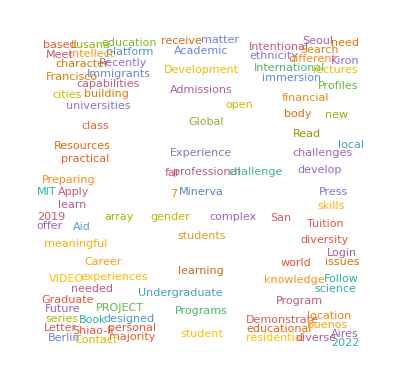

```mathematica
WordCloud[Import["http://minerva.kgi.edu"]]
```

Your turn! Import the text of your favorite website and create a word cloud.

```mathematica
(*your code goes here*)
```

### Real-World Data

You can import Data using the Import function we saw above in various forms, like csv files, images, and many more.
In addition, there is some data already built into the language, for example using the function ExampleData.

Create a word cloud of

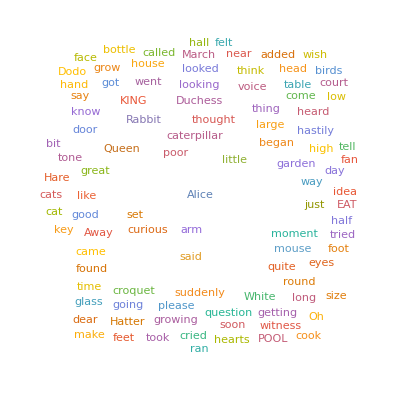

```mathematica
WordCloud[ExampleData[{"Text","AliceInWonderland"}]]
```

Wikipedia is also a great source of data. Of course you can do much more than creating word-clouds, but that’s for another time.

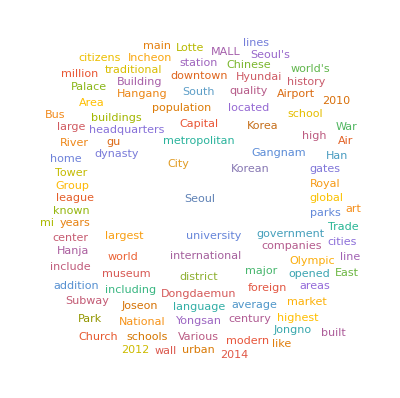

```mathematica
WordCloud[WikipediaData["Seoul"]]
```

The Wolfram Language also gives you access to the "Wolfram Knowledgebase" which has data on various topics like countries, animals, movies, people, etc.  
Sometimes it is easier to input something like in plain English. To tell the Wolfram Language that you are inputting natural language, press [CTRL] + [=]

A field like this one will pop up

```mathematica
LinguisticAssistant
```

Enter what you want to learn about and click away to get the interpretation of your input

```mathematica
LinguisticAssistant
```

Confirm that this is what you want or choose another option in the [...] menu

```mathematica
Entity["City",{"SanFrancisco","California","UnitedStates"}]
```

San Francisco is an Entity of type city and you can get all kinds of information by following the expression with [“...”]
[“Properties”] will give you all the properties of an entity type that  you can learn about.

Find out about the properties you can get about a city:

```mathematica
Entity["City",{"SanFrancisco","California","UnitedStates"}]["Properties"]
```

{administrative region,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,airport codes,fuel spent in delays,total fuel spent in delays,average annual delay,total annual delay,area,area code,arterial street traffic,arterial street length,average public transit trip distance,number of burglaries,rate of burglary,city sales tax,coordinates,country,county,county sales tax,total rate of crime,total number of crimes,average daily traffic delay,elevation,number of rapes,rate of rape,freeway traffic,freeway length,Gini index,has polygon?,FHFA home price index,FHFA home price index annual average,housing affordability index,households,number of larcenies,rate of larceny,latitude,longitude,total magnetic field strength,median age,median home sale price,median home value,median household income,number of motor vehicle thefts,rate of motor vehicle thefts,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,next daylight saving shift,nicknames,number of owner-occupied housing units,average daily peak period travelers,peak period travelers per capita,average daily peak period vehicles,notable people born in city,notable people who died in city,per capita income,polygon,city population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,last daylight saving shift,total rate of property crime,total number of property crimes,total public transit use,unlinked public transit trips,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,number of robberies,rate of robbery,daily rush hour length,state sales tax,time zone,total daily traffic delay,total sales tax rate,average peak travel time,unemployment rate,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,ZIP codes}

Ouch, I hope I’m not stirring any open wounds with this one:

```mathematica
Entity["City",{"SanFrancisco","California","UnitedStates"}]["MedianHomeSalePrice"]
```

769 600.00 $

Just imagine how powerful this kind of built-in data is if you want to compare different cities, countries, etc.
Not all the data is available for every city and you will run into problems, but it can be really useful and help you combine your own data with things like GDP, population size or other things you can come up with.
The Wolfram Language is great for math, but you can do some pretty cool Social Science or Arts and Humanities research as well. Get creative and let me know if you have an idea and want help working on it, it’s the best way for you to learn the Wolfram Language

Return the population of a city of your choice:

```mathematica
(*your code goes here*)
```

I hope you got a little bit excited to use this new tool.
Stay tuned for more notebooks and help in learning aspects of the Wolfram Language that are most relevant/useful for the Minerva curriculum.
If you want to get more resources, you can find An Elementary Introduction to the Wolfram Language and a Fast Introduction for Programmers online and pick what topics you want to learn about.